# Constant Coefficients

```mathematica
a0GaN:= Quantity[2×10^5,"Centimeter^(-1)"]
a0AlN:= Quantity[1×10^5,"Centimeter^(-1)"]
E0:=Quantity[6.424,"eV"]
AlN:=Quantity[6.28, "eV"]
GaN:=Quantity[3.44, "eV"]
AlContent:= 0.72
a0:= a0AlN *AlContent+ a0GaN*(1-AlContent)
EG:=AlN×(AlContent)+GaN(1-AlContent)

a:= a0 × √((E0-EG)/EG)
ParallelEvaluate[Off[Part::span]]
ParallelEvaluate[Off[FindFit::fitd]]
ParallelEvaluate[Off[ReplaceAll::reps]]
ParallelEvaluate[Off[Part::pkspec1]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

«1 more identical outputs»

# Graphing

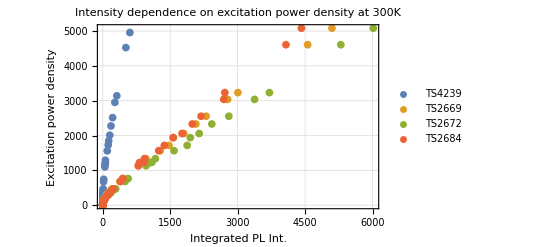
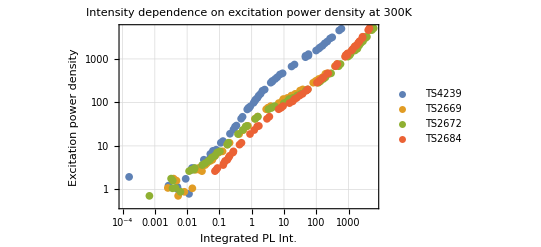

```mathematica
(*t := Import["TS2804.txt","Table"]
ListPlot[t,PlotRange-> Full, PlotLegends->{TS2804}, PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Excitation power density",20],Style["Integrated  PL Int.",20]},
PlotTheme->"Scientific"]*)
s:=N[Import["TS4239.txt","Table"]]
t:=N[Import["TS2669.txt","Table"]]
v:=N[Import["TS2672.txt","Table"]]
w:=N[Import["TS2684.txt","Table"]]
Row[{ListPlot[{s,t,v,w},PlotRange-> Full, PlotLegends->{TS4239 , TS2669, TS2672,TS2684},ImageSize->400,PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Integrated  PL Int.",20],Style["Excitation power density",20]},
PlotTheme->"Detailed"],
ListLogLogPlot[{s,t,v,w},PlotRange-> Full, PlotLegends->{TS4239 , TS2669, TS2672,TS2684}, ImageSize->400,PlotLabel-> "Intensity dependence on excitation power density at 300K",
FrameLabel->{Style["Integrated  PL Int.",20],Style["Excitation power density",20]},
PlotTheme->"Detailed"]}]
```

```mathematica
Clear[x,r]
s1 =ArrayReshape[s,{61,2}] //N;
t1 =ArrayReshape[t,{61,2}] //N;
v1 =ArrayReshape[v,{61,2}] //N;
w1 =ArrayReshape[w,{61,2}] //N;
l1=s1[[All,2]]*x*(1-r)/(QuantityMagnitude[E0])*6.241509*10^21;
l2=t1[[All,2]]*x*(1-r)/(QuantityMagnitude[E0])*6.241509*10^21;
l3=v1[[All,2]]*x*(1-r)/(QuantityMagnitude[E0])*6.241509*10^21;
l4=w1[[All,2]]*x*(1-r)/(QuantityMagnitude[E0])*6.241509*10^21;
o1=s1[[All,1]];
o2=t1[[All,1]];
o3=v1[[All,1]];
o4=w1[[All,1]];
m1:= Sort[Transpose[{o1,l1}]]
m2:=  Sort[Transpose[{o2,l2}]]
m3:=  Sort[Transpose[{o3,l3}]]
m4:=  Sort[Transpose[{o4,l4}]]

Manipulate[Row[{ListPlot[{N[m1[[ii ;; i]]],N[m2[[ii ;; i]]],N[m3[[ii ;; i]]],N[m4[[ii ;; i]]]}  /.x-> α  /.r->R,PlotRange-> Full, PlotLegends->{TS4239 , TS2669, TS2672,TS2684},
FrameLabel->{Style["Integrated  PL Int.",20],Style["Generationsrate",20]},ImageSize-> 400,
PlotTheme->"Detailed"],ListLogLogPlot[{N[m1[[ii ;; i]]],N[m2[[ii ;; i]]],N[m3[[ii ;; i]]],N[m4[[ii ;; i]]]}  /.x-> α  /.r->R,PlotRange-> Full, PlotLegends->{TS4239 , TS2669, TS2672,TS2684},ImageSize->400,
FrameLabel->{Style["Integrated  PL Int.",20],Style["Generationsrate",20]},
PlotTheme->"Detailed"]}],{α, 1*10^4, 1*10^8},{R, 0.1,1.0},{{i,50,"Anzahl Messdaten bis"},1,61,1},{{ii ,20,"Anzahl Messdaten von"},1,61,1}]
```

# Data Fitting

```mathematica
x:=1*10^5
r:=0.20






Off[Part::span]
Off[FindFit::fitd]
Off[ReplaceAll::reps]
Off[Part::pkspec1]

(*Manipulate[{IQE1 /.i ->I /.j->J,IQE2 /.i ->I /.j->J,IQE3 /.i ->I /.j->J,IQE4 /.i ->I /.j->J,Show[ListPlot[{m1[[1 ;; i]],m2[[1 ;; i]],m3[[1 ;; i]],m4[[1 ;; i]]}/.i ->I /.j->J,PlotRange-> Automatic, PlotLegends->{TS2804 swap}],Plot[ { a1*√p+a2*p,b1*√p+b2*p, c1*√p+c2*p,d1*√p+d2*p}/.i-> I /.j->J ,{p,0,600},PlotRange->Automatic]]},{{J,10,"Messpunkt"},1,60,1},{{I,50,"Anzahl Messdaten"},1,60,1}]*)



Manipulate[
par1=FindFit[(#),z1*√y+ z2 * 10^y,{z1,z2},y]&/@{m1[[II ;; IJ]],m2[[II ;; IJ]],m3[[II ;; IJ]],m4[[II ;; IJ]]};
a1=(z1/.par1[[1]]);
a2=(z2/.par1[[1]]);
b1=(z1/.par1[[2]]);
b2=(z2/.par1[[2]]);
c1=(z1/.par1[[3]]);
c2=(z2/.par1[[3]]);
d1=(z1/.par1[[4]]);
d2=(z2/.par1[[4]]);
Column[{
Show[ListPlot[{m1[[II ;; IJ]],m2[[II ;; IJ]],m3[[II ;; IJ]],m4[[II ;; IJ]]},PlotLegends->{TS4239 , TS2669, TS2672,TS2684},PlotTheme-> "Detailed",ImageSize->400],Plot[ { a1*√p+a2*p,b1*√p+b2*p, c1*√p+c2*p,d1*√p+d2*p} ,{p,0,6000},PlotRange->Full]] ,Show[ListLogLogPlot[{m1[[II ;; IJ]],m2[[II ;; IJ]],m3[[II ;; IJ]],m4[[II ;; IJ]]},PlotLegends->{TS4239 , TS2669, TS2672,TS2684},PlotTheme-> "Detailed",ImageSize->400],LogLogPlot[ { a1*√p+a2*p,b1*√p+b2*p, c1*√p+c2*p,d1*√p+d2*p}  ,{p,1*10^-5,6000},PlotRange->Full]]
}]
,{{II,20,"Anzahl Messdaten bis"},1,61,1},{{IJ,50,"Anzahl Messdaten von"},1,61,1}
]
```

```mathematica
Manipulate[
par=FindFit[({Log10[#[[1]]],Log10[#[[2]]]}&/@#),Log10[10^z1*√(10^y)+10^ z2 * 10^y],{z1,z2},y]&/@{m1[[II ;; IJ]],m2[[II ;; IJ]],m3[[II ;; IJ]],m4[[II ;; IJ]]};
a1p=10^(z1/.par[[1]]);
a2p=10^(z2/.par[[1]]);
b1p=10^(z1/.par[[2]]);
b2p=10^(z2/.par[[2]]);
c1p=10^(z1/.par[[3]]);
c2p=10^(z2/.par[[3]]);
d1p=10^(z1/.par[[4]]);
d2p=10^(z2/.par[[4]]);
Column[{
Show[ListPlot[{m1[[II ;; IJ]],m2[[II ;; IJ]],m3[[II;;IJ]],m4[[II ;; IJ]]},PlotLegends->{TS4239 , TS2669, TS2672,TS2684},PlotTheme-> "Detailed",ImageSize->400],Plot[ { a1p*√p+a2p*p,b1p*√p+b2p*p, c1p*√p+c2p*p,d1p*√p+d2p*p} ,{p,0,6000},PlotRange->Full]],
Show[ListLogLogPlot[{m1[[II ;; IJ]],m2[[II ;; IJ]],m3[[II;;IJ]],m4[[II ;; IJ]]},PlotLegends->{TS4239 , TS2669, TS2672,TS2684},PlotTheme-> "Detailed",ImageSize->400],LogLogPlot[ { a1p*√p+a2p*p,b1p*√p+b2p*p, c1p*√p+c2p*p,d1p*√p+d2p*p} ,{p,1*10^-5,6000},PlotRange->Full]]
}]
 ,{{IJ,50,"Anzahl Messdaten"},1,60,1},{{II,20,"Anzahl Messdaten von"},1,60,1}]
```

```mathematica
x:=1*10^5
r:=0.20

ai=25; {Slider[Dynamic[ai],{1,60,1}],Dynamic[ai]}
bi=50;{Slider[Dynamic[bi],{30,60,1}],Dynamic[bi]}
```

{,}

{,}

{0.0126032,0.0139344,0.0203072,0.0219712,0.0216904,0.0236742,0.0283697,0.0312323,0.0332242,0.0359833,0.04035,0.0442227,0.0511937,0.0541226,0.0746441,0.0787584,0.0806967,0.0880956,0.0952585,0.107236,0.112804,0.148949,0.160663,0.210057,0.21962,0.221482}

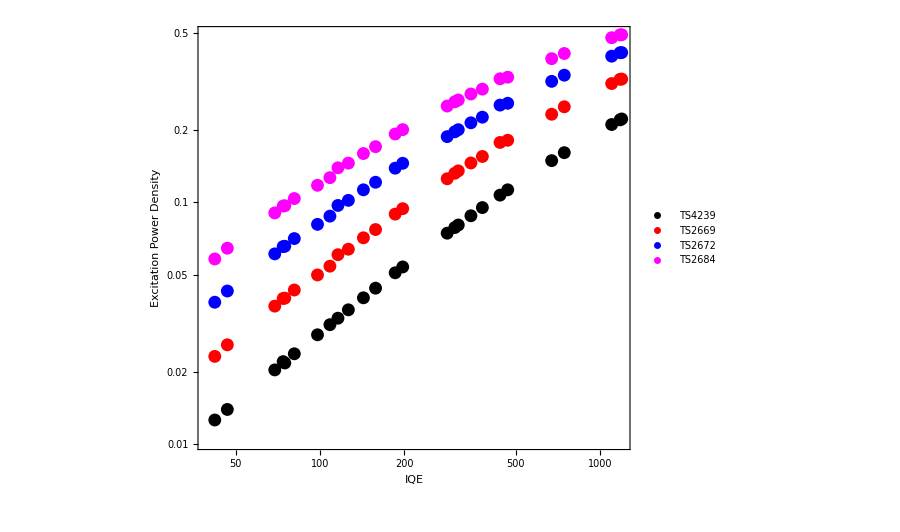

```mathematica
fitting[m_] :=FindFit[m[[ai;;bi,All]],z1*√y+ z2 * y,{z1,z2},y]


par:=ParallelMap[fitting,{m1,m2,m3,m4}]



a1=(z1/.par[[1]]);
a2=(z2/.par[[1]]);
b1=(z1/.par[[2]]);
b2=(z2/.par[[2]]);
c1=(z1/.par[[3]]);
c2=(z2/.par[[3]]);
d1=(z1/.par[[4]]);
d2=(z2/.par[[4]]);

Erg1:=Solve[a1/√a2*B1 + B1^2 == m1[[n,2]],B1]
Erg2:=Solve[b1/√b2*B2 + B2^2 == m2[[n,2]],B2]
Erg3:=Solve[c1/√c2*B3 + B3^2 == m3[[n,2]],B3]
Erg4:=Solve[d1/√d2*B4 + B4^2 == m4[[n,2]],B4]

Ergebnisse :=ParallelTable[{Erg1[n],Erg2[n],Erg3[n],Erg4[n]},{n,ai,bi,1}]

a11=B1/.Ergebnisse[[;;,1,0,2]];
a12=B2/.Ergebnisse[[;;,2,0,2]];
a13=B3/.Ergebnisse[[;;,3,0,2]];
a14=B4/.Ergebnisse[[;;,4,0,2]];


IQE1Tab = a11[[;;]]^2/m1[[ai;; bi,2]]
IQE2Tab = a12[[;;]]^2/m2[[ai;;bi,2]];
IQE3Tab = a13[[;;]]^2/m3[[ai;; bi,2]];
IQE4Tab= a14[[;;]]^2/m4[[ai;; bi,2]];


snew=Sort[s[[;;,2]]];
snew1= snew[[ai;;bi]];
t11=Transpose[{snew1,IQE1Tab}];
t12=Transpose[{snew1,IQE2Tab}];
t13=Transpose[{snew1,IQE3Tab}];
t14=Transpose[{snew1,IQE4Tab}] ;


ListLogLogPlot[{t11,t12,t13,t14} ,PlotLegends->Placed[{TS4239 , TS2669, TS2672,TS2684},{0.85,0.25}],PlotStyle->{Black, Red,Blue, Magenta},PlotRange->Full, PlotTheme->"Detailed",AspectRatio-> 0.8/1,AxesLabel->{"IQE","Excitation Power Density"}]
```

{0.133059,0.176735,0.206078,0.226254,0.235372,0.290708,0.307343,0.372453,0.386476,0.384179,0.399857,0.432543,0.449995,0.461231,0.475727,0.496503,0.513069,0.539366,0.549294,0.605729,0.614968,0.619137,0.634078,0.647258,0.666982,0.675319,0.720113,0.732029,0.773302,0.780027,0.781298}

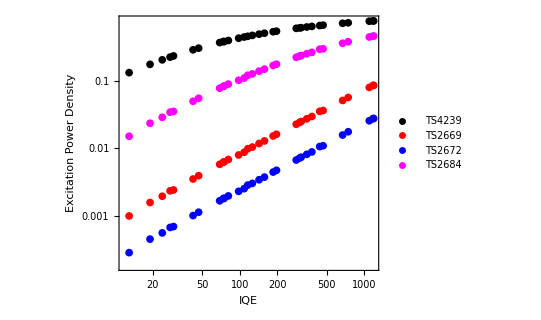

```mathematica
(*fitting[m_] :=FindFit[m[[ai;;bi,All]],z1*√y+ z2 * y,{z1,z2},y]*)


par2=FindFit[({Log10[#[[1]]],Log10[#[[2]]]}&/@#),Log10[10^z1*√(10^y)+10^ z2 * 10^y],{z1,z2},y]&/@{m1[[ai ;; bi]],m2[[ai;; bi]],m3[[ai ;;bi]],m4[[ai ;;bi]]};


a1p=10^(z1/.par2[[1]]);
a2p=10^(z2/.par2[[1]]);
b1p=10^(z1/.par2[[2]]);
b2p=10^(z2/.par2[[2]]);
c1p=10^(z1/.par2[[3]]);
c2p=10^(z2/.par2[[3]]);
d1p=10^(z1/.par2[[4]]);
d2p=10^(z2/.par2[[4]]);




Erg1:=Solve[a1p/√a2p*B1 + B1^2 == m1[[n,2]],B1]
Erg2:=Solve[b1p/√b2p*B2 + B2^2 == m2[[n,2]],B2]
Erg3:=Solve[c1p/√c2p*B3 + B3^2 == m3[[n,2]],B3]
Erg4:=Solve[d1p/√d2p*B4 + B4^2 == m4[[n,2]],B4]

Ergebnisse :=ParallelTable[{Erg1[n],Erg2[n],Erg3[n],Erg4[n]},{n,ai,bi,1}]

a11=B1/.Ergebnisse[[;;,1,0,2]];
a12=B2/.Ergebnisse[[;;,2,0,2]];
a13=B3/.Ergebnisse[[;;,3,0,2]];
a14=B4/.Ergebnisse[[;;,4,0,2]];


IQE1Tab = a11[[;;]]^2/m1[[ai;; bi,2]]
IQE2Tab = a12[[;;]]^2/m2[[ai;;bi,2]];
IQE3Tab = a13[[;;]]^2/m3[[ai;; bi,2]];
IQE4Tab= a14[[;;]]^2/m4[[ai;; bi,2]];


snew=Sort[s[[;;,2]]];
snew1= snew[[ai;;bi]];
t11=Transpose[{snew1,IQE1Tab}];
t12=Transpose[{snew1,IQE2Tab}];
t13=Transpose[{snew1,IQE3Tab}];
t14=Transpose[{snew1,IQE4Tab}] ;


ListLogLogPlot[{t11,t12,t13,t14} ,PlotLegends->Placed[{TS4239 , TS2669, TS2672,TS2684},{0.85,0.25}],PlotStyle->{Black, Red,Blue, Magenta},PlotRange->Full, PlotTheme->"Detailed",AspectRatio-> 0.8/1,AxesLabel->{"IQE","Excitation Power Density"}]
```

{z1→27.4125,z2→26.2386}

2.58539×10^27

10^z2

{{-0.286997,27.5262},{-0.160698,27.5627},{0.244012,27.7398},{0.331595,27.8123},{0.333177,27.7804},{0.434433,27.8489},{0.620073,27.8871},{0.731539,27.9304},{0.826416,27.9773},{0.899917,28.0047},{1.01944,28.0635},{1.1042,28.1008},{1.26049,28.1736},{1.29418,28.2023},{1.5952,28.3605},{1.64588,28.3919},{1.66399,28.4026},{1.73916,28.4414},{1.79733,28.4893},{1.92504,28.5608},{1.93029,28.5803},{2.18437,28.7436},{2.23947,28.78},{2.47422,28.9572},{2.52236,28.9979},{2.54415,29.0297}}

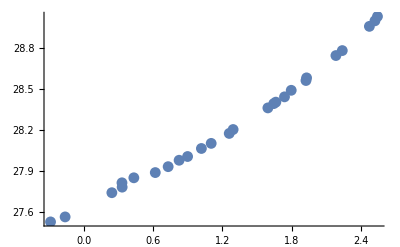

```mathematica
para=FindFit[Log10[m1],Log10[10^z1*√(10^y)+10^z2 *10^y],{z1,z2},y]

a1p=10^(z1/.par[[1]])
a2p=10^(z2/.par[[1]])

Log10[m1[[ai;;bi,;;]]]

ListPlot[Log10[m1[[ai;;bi,;;]]]]
```